## Теоретическая оценка на концентрацию и поток

```mathematica
kB= 1.38 10^-23;
ℏ = 1.054571817 10^-34;
Na = 6.02 10^23;
m = 0.007 / Na;
Snoz = 40;
```

```mathematica
ClearAll[GetP, GetNin, GetNout];
GetP[T_] := 133.32 10^(10.3454 -8345.57/T-8.84 10^-5 T - 0.68106 Log10[T]);
GetNin[T_] := GetP[T]/(kB T);
```

```mathematica
GetNin[273+400]
```

1.3071×10^18

```mathematica
ScientificForm[(1-Cos[7/(2 210)]) // N]
```

1.38886×10^-4

```mathematica
θmax = 7/(2 210);
```

## Оценка из Duke Uni

```mathematica
int1 = Integrate[vr vz ⅇ^(-vr^2/α^2)  ⅇ^(-vz^2/α^2), {vr, 0, ∞}, {vz, 0, ∞}, Assumptions->α >0]
```

α^4/4

```mathematica
2/(√π)int1/α^3 /. {α-> (√π)/2 vbar}
```

vbar/4

```mathematica
int2 = FullSimplify@Integrate[
vr vz ⅇ^(-vr^2/α^2)  ⅇ^(-vz^2/α^2) HeavisideTheta[θ- vr/vz]
, {vr, 0, ∞}, Assumptions->α >0 && θ>0 && vz > 0]
```

1/2 ⅇ^(-vz^2/α^2) (1-ⅇ^(-(vz^2 θ^2)/α^2)) vz α^2

```mathematica
(*2/(√π)int2/α^3 /. {α-> (√π)/2 vbar}*)
```

```mathematica
Normal@Series[(1-Cos[θ]), {θ,0, 2}]
```

θ^2/2

## !Итоговое количество на выходе

```mathematica
kB= 1.38 10^-23;
ℏ = 1.054571817 10^-34;
Na = 6.02 10^23;
m = 0.007 / Na;
```

```mathematica
θmax = 7./(2 210);
Snoz = 40. 10^-6;
```

```mathematica
ClearAll[GetP, GetVbar, GetNin, GetNout, GetT];
GetP[T_] := 133.32 10^(10.3454 -8345.57/T-8.84 10^-5 T - 0.68106 Log10[T]);
GetNin[T_] := GetP[T]/(kB T);
GetVbar[T_] := √((8 kB T)/(π m));
GetNout[T_] := Snoz 1/4 GetNin[T] GetVbar[T] θmax^2;
GetT[T1_, T2_] := 0.1 T1 + 0.9 T2;
```

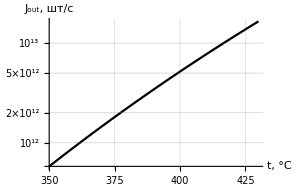

```mathematica
img = LogPlot[GetNout[273+t], {t, 350, 430}, GridLines->Automatic, PlotStyle->Black, AxesLabel->{"t, °C", "J_out, шт/c"}, ImageSize->150{2, 1}]
(*Export[NotebookDirectory[]<>"figures/"<>"j_out_theor.pdf", img]*)
```

## Draft

```mathematica
GetNout[273+GetT[421,375]]/GetNout[273+GetT[373,345]]
```

4.23282

```mathematica
GetNout[273+416]
```

9.74259×10^12

```mathematica
GetNout[273+375]/GetNout[273+345]
```

3.96485

```mathematica
GetNout[273+375]
GetNout[273+GetT[421,375]]
GetNout[273+421]
```

1.80877×10^12

2.20867×10^12

1.17975×10^13